```mathematica
solveKepler[x0_,y0_,vx0_,vy0_,t0_,tf_]:=Module[
{γ=39.42(*field strength in AU^3/Year^2*)},
{{x[t],y[t]}/.NDSolve[{x''[t]+(γ( x[t]))/((x[t]^2+y[t]^2)^(3/2))==0,y''[t]+(γ( y[t]))/((x[t]^2+y[t]^2)^(3/2))==0,x'[t0]==vx0,x[t0]==x0,y'[t0]==vy0,y[t0]==y0},{x[t],y[t]},{t,t0,tf}]//Flatten,t0<t<=tf}]
solveKepler3D[x0_,y0_,vx0_,vy0_,t0_,tf_]:=Module[
{γ=39.42(*field strength in AU^3/Year^2*)},
{{x[t],y[t],0}/.NDSolve[{x''[t]+(γ( x[t]))/((x[t]^2+y[t]^2)^(3/2))==0,y''[t]+(γ( y[t]))/((x[t]^2+y[t]^2)^(3/2))==0,x'[t0]==vx0,x[t0]==x0,y'[t0]==vy0,y[t0]==y0},{x[t],y[t]},{t,t0,tf}]//Flatten,t0<t<=tf}]
```

```mathematica
circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

Define celestial bodies

```mathematica
Planet[t_,orbitR_,bodyR_,color_,τ_,ϕ_:0]:={color,Disk[orbitR*{Cos[2*Pi/τ*t+ϕ],Sin[2*Pi/τ*t+ϕ]},bodyR],Black,Thin,Circle[{0,0},orbitR]};
```

```mathematica
Planet3D[t_,orbitR_,bodyR_,color_,τ_,ϕ_:0]:={color,Sphere[orbitR*{Cos[2*Pi/τ*t+ϕ],Sin[2*Pi/τ*t+ϕ],0},bodyR],White,circle3D[{0,0,0},orbitR]};
```

```mathematica
(*Units: Time -> Earth Year, Distance -> AU*)
```

```mathematica
Sun={Yellow,Disk[{0,0},.2]};
```

```mathematica
(*Planet data lookup*)
```

```mathematica
earthRadius = 0.05;
```

```mathematica
Earth[t_]:=Planet[t,1,earthRadius,Blue,1];
Mercury[t_]:=Planet[t,0.374496,earthRadius*0.38,RGBColor[0.30519228864556863, 0.305192033330491, 0.3051918991832576],0.241,Pi/2];
Mars[t_]:=Planet[t,1.5458,earthRadius*0.53,RGBColor[0.7251083999292833, 0.44716417625377575, 0.3841326243958847],1.8821,Pi+.7];
Venus[t_]:=Planet[t,0.726088,earthRadius*0.95,RGBColor[0.7515883723488025, 0.32365215466317643, 0.13040807232115398],0.6156,3Pi/4];
Jupiter[t_]:=Planet[t,5.328,earthRadius*3,Red,11.87,Pi/2+.38];
```

```mathematica
(*Animate the solar system for one earth year*)
```

```mathematica
height=1;
```

```mathematica
AUSolarSystem[t_]:=Graphics[{Sun,Earth[t],Venus[t],Mercury[t],Mars[t],Jupiter[t]}//Flatten,AspectRatio->9/16,Axes->False,PlotRange->{{-height*16/9*10(1-E^(-t/5)),height*16/9*10(1-E^(-t/5))},{-height*10(1-E^(-t/5))+t/6,height*10(1-E^(-t/5))+t/6}},Background->White];
Animate[AUSolarSystem[t],{t,0,5.5}]
```

```mathematica
(*Earth intial velocity in AU/Year*)
```

```mathematica
D[Earth[t][[2]][[1]],t]/.{t->0}
```

{0,2 π}

```mathematica
(*Trajectory, a good proof that this simulator is accurate is to set the probe velocity to exactly that of earths and notice that the kepler solver makes it follow exactly earths orbit*)
```

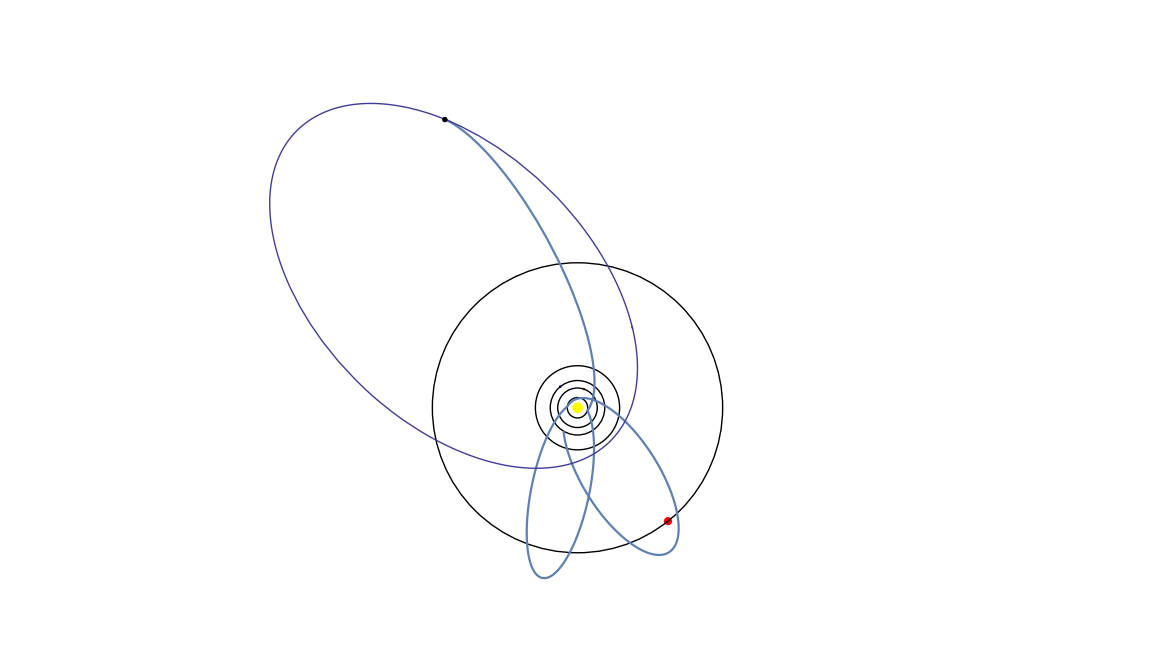

```mathematica
pos=<|1->{-0.5108553416136539,-0.8596666911918811},2->{-0.37183505997239796,0.04456391131087142},3->{0.3590219296243132,-0.10653876320304602}|>;
times=<|1->0.6646643877033261,2->6.562674868176869,3->12.460685348650411,4->18.358695829123953|>;
vels=<|1->{0.7650395576494904,-8.142046091626291},2->{-11.182182664371702,-8.571363648378641},3->{8.882121349697794,11.193467870583913}|>;

(*pos=<|1->{1,0},2->{0.9842,0.0833},3->{-0.395,1.4912}|>;
times = <|1->0,2->1,3->1.28,4->5.5|>;
vels=<|1->{-.9,2*Pi-.1},2->{-1.5,8},3->{-5.848-1/3,1.3259}|>;*)
solution=Table[solveKepler[pos[i][[1]],pos[i][[2]],vels[i][[1]],vels[i][[2]],times[i],times[i+1]],{i,1,Length[pos]}]//Piecewise;
Show[AUSolarSystem[times[Length[times]]],ParametricPlot[solution,{t,times[1],times[Length[times]]}],ParametricPlot[comet[[1]]/.{t->s},{s,0,23.1},PlotStyle->Directive[Hue[0.67,0.6,0.6],Thin]],
Graphics[Disk[comet[[1]]/.t->times[Length[times]],.1]]
]
```

```mathematica
comet = solveKepler[2,3,1,-4,0,30]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},0<t≤30}

```mathematica
c[s_]:=comet[[1]]/.t->Mod[s+2.2,23.1]
```

```mathematica
(*,*)
```

```mathematica
Animate[Show[
AUSolarSystem[s],
ParametricPlot[solution//Evaluate,{t,times[1],s}],
ParametricPlot[c[s],{t,0,23.1},PlotStyle->Directive[Hue[0.67,0.6,0.6],Thin]
],
Graphics[
Disk[c[s],.1]]
],{s,times[1]+0.00001,times[Length[times]],0.004},AnimationRepetitions->1]
```

```mathematica
(*Generate frames*)
```

```mathematica
frames = Table[
Show[
AUSolarSystem[s],
ParametricPlot[solution//Evaluate,{t,0,s}]
],
{s,0.0088,5.5,0.01716}];
```

```mathematica
exportFolder="~/Desktop/jupiterbest/";
videoname = "jupiterlaunchbest";
```

```mathematica
(*Run this to generate the video*)
```

```mathematica
Table[Export[StringForm[exportFolder<>"image``.png",IntegerString[i,10,5]]//ToString,frames[[i]],ImageResolution->350],{i,1,Length[frames]}];
```

```mathematica
"cd "<>exportFolder<>" && ffmpeg -f image2 -r 30 -i image%05d.png -vcodec mpeg4 -y "<>videoname<>".mp4"//ToString
```

cd ~/Desktop/jupiter3d/ && ffmpeg -f image2 -r 30 -i image%05d.png -vcodec mpeg4 -y jupiterlaunch3d.mp4

```mathematica
"ffmpeg -f image2 -r 30 -i image%05d.png -vcodec mpeg4 -y "<>videoname<>".mp4"
```

ffmpeg -f image2 -r 30 -i image%05d.png -vcodec mpeg4 -y jupiterlaunch.mp4

```mathematica
Sun3D={Yellow,Sphere[{0,0,0},.2]};
```

```mathematica
Earth3D[t_]:=Planet3D[t,1,earthRadius,Blue,1];
Mercury3D[t_]:=Planet3D[t,0.374496,earthRadius*0.38,RGBColor[0.30519228864556863, 0.305192033330491, 0.3051918991832576],0.241,Pi/2];
Mars3D[t_]:=Planet3D[t,1.5458,earthRadius*0.53,RGBColor[0.7251083999292833, 0.44716417625377575, 0.3841326243958847],1.8821,Pi+.7];
Venus3D[t_]:=Planet3D[t,0.726088,earthRadius*0.95,RGBColor[0.7515883723488025, 0.32365215466317643, 0.13040807232115398],0.6156,3Pi/4];
Jupiter3D[t_]:=Planet3D[t,5.328,earthRadius*3,Red,11.87,Pi/2+.38];
```

```mathematica
AUSolarSystem3D[t_]:=Graphics3D[{Sun3D,Earth3D[t],Venus3D[t],Mercury3D[t],Mars3D[t],Jupiter3D[t]},Boxed->False,ViewCenter->{0.5, 0.5, 0.5},ViewVector->{1.5+t,1.5+t/4,1.2*t+.3},Background->Black,AspectRatio->1];
Animate[AUSolarSystem3D[t],{t,0,5.5}]
```

```mathematica
solution3D=Table[solveKepler3D[pos[i][[1]],pos[i][[2]],vels[i][[1]],vels[i][[2]],times[i],times[i+1]],{i,1,Length[pos]}]//Piecewise;
```

```mathematica
(*ParametricPlot3D[comet[[1]],{t,0,23.1},PlotStyle->Directive[Hue[0.67,0.6,0.6],Dashed]],
Graphics3D[Sphere[comet[[1]]/.t->Mod[s,23.1],.1]]*)
```

```mathematica
Animate[
Show[
AUSolarSystem3D[s],
ParametricPlot3D[solution3D//Evaluate,{t,times[1],s},PlotStyle->{RGBColor[0.16,0.94,0.34]}]
]
,{s,times[1]+0.0001,times[Length[times]]},
AnimationRepetitions->1,DefaultDuration->25]
```

```mathematica
frames = Table[frame[s],{s,0.01,5.5,0.02745}]
```

```mathematica
frame[s_]:=Show[AUSolarSystem3D[s],ParametricPlot3D[solution//Evaluate,{t,0,s},PlotStyle->{Thickness[.008],RGBColor[1,1,1]}]]
```

```mathematica
Cyan
```

RGBColor[0, 1, 1]

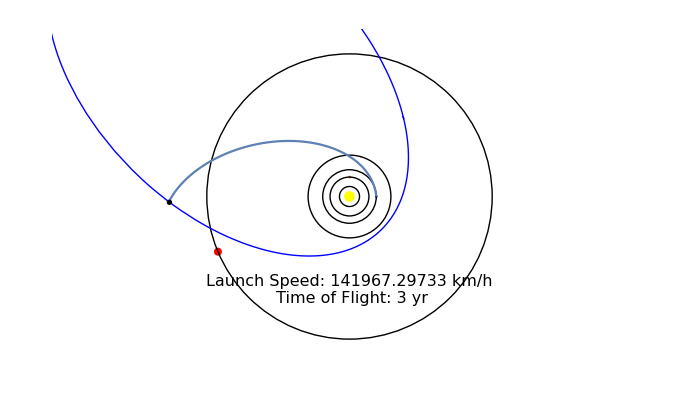

```mathematica
Show[
AUSolarSystem[3],ParametricPlot[solveKepler[1,0,-0.77360159, 8.27710375,0,2][[1]]/.{t->s},{s,0,3}],Graphics[Text[Style["Launch Speed: 141967.29733 km/h\n Time of Flight: 3 yr",FontFamily->"CMU Serif",FontSize->16],{0,-3.5}]],
ParametricPlot[
comet[[1]],{t,0,23.1},PlotStyle->Directive[Blue,Thin]
],
Graphics[
Disk[comet[[1]]/.t->3,.1]
]
]
```

```mathematica
planets={"Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune"}
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
elements=Table[{QuantityMagnitude[PlanetData[p,"SemimajorAxis"]],QuantityMagnitude[PlanetData[p,"SemiminorAxis"]]},{p,planets}]
```

{{0.3870989,0.3788265},{0.723332,0.7233154},{1.0000001,0.99986048},{1.5236623,1.5170001},{5.203363,5.1972667},{9.5370703,9.5230773},{30.0689635,30.0678552},{19.1912639,19.1699037}}

```mathematica
p[{a_,b_}]:=b^2/a;
```

```mathematica
e[{a_,b_}]:=Sqrt[1-(b/a)^2]
```

```mathematica
orbit[t_,params_]:=p[params]/(1-Cos[t]*e[params])*{Sin[t],Cos[t]}
```

```mathematica
GraphicsRow[{ParametricPlot[Table[orbit[t,elm],{elm,elements[[1;;4]]}]//Evaluate,{t,0,2*Pi},AxesLabel->{"AU","AU"},LabelStyle->{FontFamily->"CMU Serif",FontColor->Black},PlotLegends->planets[[1;;4]],PlotRange->Full,PlotLabel->"Inner Solar System"],ParametricPlot[Table[orbit[t,elm],{elm,elements}]//Evaluate,{t,0,2*Pi},AxesLabel->{"AU","AU"},LabelStyle->{FontFamily->"CMU Serif",FontColor->Black},PlotLabel->"Outer Solar System",PlotLegends->planets,PlotRange->Full]},PlotLabel->"The Solar System",LabelStyle->{FontFamily->"CMU Serif",FontSize->16,FontColor->Black}]
```

-Graphics-

```mathematica
Table[planets[[i]]->elements[[i]][[1]]/elements[[i]][[2]],{i,1,elements//Length}]
```

{Mercury→1.021837,Venus→1.000023,Earth→1.0001396,Mars→1.0043917,Jupiter→1.001173,Saturn→1.0014694,Uranus→1.00003686,Neptune→1.00111426}

```mathematica
Table[comet[[1]][[2]],{t,2.2,23.1+2.2,.1}]
```

{-1.41627,-1.27199,-1.12412,-0.973459,-0.820679,-0.66631,-0.510784,-0.354459,-0.197631,-0.0405458,0.11659,0.273602,0.430343,0.586687,0.742529,0.897775,1.05235,1.20618,1.35922,1.5114,1.66269,1.81306,1.96245,2.11086,2.25825,2.4046,2.54989,2.69411,2.83725,2.97928,3.1202,3.26,3.39867,3.53621,3.67261,3.80786,3.94195,4.0749,4.20668,4.3373,4.46676,4.59506,4.72218,4.84814,4.97293,5.09654,5.21899,5.34026,5.46035,5.57928,5.69703,5.8136,5.929,6.04323,6.15628,6.26815,6.37884,6.48836,6.5967,6.70387,6.80985,6.91466,7.01828,7.12073,7.22199,7.32207,7.42097,7.51868,7.61521,7.71055,7.8047,7.89766,7.98943,8.08,8.16938,8.25757,8.34455,8.43033,8.5149,8.59827,8.68043,8.76137,8.8411,8.91961,8.99689,9.07296,9.14779,9.22138,9.29374,9.36486,9.43473,9.50336,9.57072,9.63683,9.70167,9.76524,9.82754,9.88855,9.94828,10.0067,10.0638,10.1197,10.1742,10.2274,10.2793,10.3298,10.379,10.4268,10.4733,10.5184,10.5622,10.6045,10.6455,10.685,10.7232,10.7599,10.7952,10.8291,10.8614,10.8924,10.9218,10.9498,10.9762,11.0011,11.0245,11.0464,11.0667,11.0854,11.1025,11.1181,11.132,11.1443,11.1549,11.1638,11.1711,11.1766,11.1804,11.1825,11.1827,11.1812,11.1779,11.1728,11.1657,11.1568,11.146,11.1332,11.1185,11.1017,11.083,11.0622,11.0392,11.0142,10.987,10.9576,10.926,10.8921,10.8559,10.8173,10.7764,10.733,10.6871,10.6387,10.5877,10.534,10.4776,10.4185,10.3565,10.2917,10.2239,10.153,10.0791,10.002,9.92155,9.83779,9.75057,9.65979,9.56537,9.46717,9.36509,9.259,9.14877,9.03426,8.91531,8.79177,8.66347,8.53021,8.3918,8.24803,8.09866,7.94345,7.78212,7.61438,7.43992,7.25837,7.06936,6.87247,6.66722,6.45312,6.22957,5.99594,5.75153,5.49552,5.22701,4.94497,4.64823,4.33546,4.00512,3.65548,3.28457,2.89015,2.46982,2.02115,1.54208,1.03194,0.493493,-0.0631393,-0.614953,-1.12374,-1.54684,-1.85913,-2.06267,-2.17602,-2.22064,-2.21451,-2.17112,-2.10016,-2.00856,-1.90136,-1.78223,-1.65389,-1.51842,-1.37739}